```mathematica
(*Read 15 for station locations*)
fpath15="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\Run 3 - 20 1 1 as DRAMP\\spindown.15";

s15=OpenRead[fpath15];
raw=ReadList[s15,String];

Close[s15];
"Use this scroll bar to find the line # of first + last stations ('start' & 'end')"
Manipulate[raw[[i]],{i,1,Length[raw],1}]
```

Use this scroll bar to find the line # of first + last stations ('start' & 'end')

```mathematica
start=958;
end=2236;


nstations=end-start+1;
(*
n61header=908;
n61headerstations=start-n61header;
n62header=;
n62stationstart=;
n62header=;
*)



stationlat=Table[0,{nstations}];
stationlon=Table[0,{nstations}];

s15=OpenRead[fpath15];
Skip[s15,String,(start-1)];

Do[
stationlon[[i]]=Read[s15,Number];
stationlat[[i]]=Read[s15,Number];
,{i,1,nstations}];

t=Read[s15,String];

Close[s15]
```

C:\Users\Sam\Desktop\Thesis Work\Irene\Run 3 - 20 1 1 as DRAMP\spindown.15

```mathematica
(*Next step is to split up stations into cross-sections. There're a few ways to do this; this method uses a csv consisting of a header row, then the x-section lat/long values, separated by two columns containing "-1" between each x-section*)
fpathxsec="C:\\Users\\Sam\\Desktop\\Thesis Work\\HEC-RAS\\main channel user defined.txt";
sxsec=OpenRead[fpathxsec];
raw=ReadList[sxsec,String];
filelength=Length[raw];
Close[sxsec];

(*!!!! Hardwired for what I know the length to be. Use above script to "guess" at file length*)
filelength=588;
sxsec=OpenRead[fpathxsec];
Read[sxsec,String];

lenlist={};
L=0;
Do[
L=L+1;
c1=Read[sxsec,Word]//ToExpression;
c2=Read[sxsec,Word]//ToExpression;
If[{c1,c2}=={-1,-1},
L=L-1;
lenlist=Flatten[Append[lenlist,L]];
L=0;
];
,{i,2,filelength}];
Close[sxsec];
```

```mathematica
(* "lenlist" is the list of x-section "lengths," in number of stations*)
nsections=Length[lenlist];
sectionlatlongs=Table[Table[0,{lenlist[[i]]}],{i,1,nsections}];

sxsec=OpenRead[fpathxsec];
Skip[sxsec,String];
Do[
Do[

c1=Read[sxsec,Word]//ToExpression;
c2=Read[sxsec,Word]//ToExpression;

sectionlatlongs[[j,i]]={c1,c2};
,{i,1,lenlist[[j]]}];
Skip[sxsec,String];
,{j,1,nsections}];

Close[sxsec];
```

```mathematica
(* convert lat/longs into x/y *)
slam0=-79.0;(*center longitude*)
sfea0=35.0;(*center latitude*)
NAN="NAN";(*Designator for non-values*)

d2r=3.14159265358979323/180;
R=6378206.4;
slam0r=slam0*d2r;
sfea0r=sfea0*d2r;
```

```mathematica
sectionxys=Table[Table[0,{lenlist[[i]]}],{i,1,nsections,1}];
Do[
Do[
lon=sectionlatlongs[[j,i,1]];
lat=sectionlatlongs[[j,i,2]];
slam=lon*d2r;
x=R*(slam-slam0r)*Cos[sfea0r];
sfea=lat*d2r;
y=R*sfea;
sectionxys[[j,i]]={x,y};
,{i,1,lenlist[[j]]}];
,{j,1,nsections}];
```

```mathematica
(*read station bathymetries*)
z=ReadList["C:\\Users\\Sam\\Desktop\\Thesis Work\\Data reading - bathymetries\\stationBathy.txt"];
sectionzs=Table[Table[0,{lenlist[[i]]}],{i,1,nsections,1}];

n=1;
Do[
Do[
sectionzs[[j,i]]=z[[n]];
n=n+1;
,{i,1,lenlist[[j]]}];
,{j,1,nsections}];
```

```mathematica
sectionxs=Flatten[sectionxys];
sectionxs=Partition[sectionxs,2];
sectionys=Transpose[sectionxs][[2]];
sectionxs=Transpose[sectionxs][[1]];
```

```mathematica
Length[Flatten[sectionzs]]
```

486

total number of stations is based on i,j,x

```mathematica
i=2;
Sum[
(lenlist[[x]]-1)*(i+1)+1
,{x,1,Length[lenlist]}]
```

1266

```mathematica
lenlist
```

{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,8,7,7,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
Sum[lenlist[[i]],{i,1,Length[lenlist]}]
```

486

```mathematica
(*Read 61 timestep for depths*)

(*Read 62 timestep for Vs*)

(*Write x-section flux out to .txt file*)
```

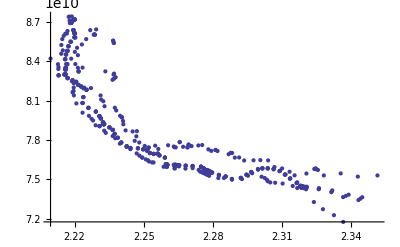

Part::partd: Part specification sectionxys ⟦ 96 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: sectionxys ⟦ 96 ⟧ is not a list of numbers or pairs of numbers.

```mathematica
ListPlot[Partition[Flatten[sectionxys],2]]
Manipulate[ListPlot[Partition[Flatten[sectionxys[[i]]],2],PlotRange->{{2.2*10^11,2.4*10^11},{7*10^10,9*10^10}}],{i,1,nsections,1}]
```

```mathematica
sfea
```

11250.954153661727

```mathematica
lenlist[[1]]
```

5

```mathematica
tempdump[[7]]=={-1,-1};
```

True

Part::partd: Part specification $Failed ⟦ 2236 ⟧ is longer than depth of object.